```mathematica
(*Quit[]*)
Clear["Global`*"]
```

Antagonistic Specialization Adaptive Dynamics. We begin by defining the change in frequency of each strategist type over time:

```mathematica
(*To begin we first define the payoffs received by hosts and symbionts*)
(*x -> the proportion of a host's resource that is shared*)
(*α -> the matched exchange rate*)
(*αg -> the generalist exchange rate*)
(*γ -> the efficiency of exchange, monotypic*)
pi=x*(α*γ−x); (*Host matched payoff*)
pi2=x*(fα*γ−x);(*Host mis-matched payoff*)
pig=x*(αg*γ−x);(*Generalist host payoff*)
ψ=x*γ*(1−α);(*Symbiont matched payoff*)
ψ2=x*γ*(1−fα);(*Host mis-matched payoff*)
ψg=x*γ*(1−αg); (*Symbiont payoff from interaction with generalist host*)
```

```mathematica
(*v1 = frequency of host 1*)
(*v2 = frequency of host 2*)
S1 = v1*ψ+v2*ψ2+(1−v1−v2)*ψg;(*Symbiont 1 Average Payoff*)
S2 = v1*ψ2+v2*ψ+(1−v1−v2)*ψg;(*Symbiont 2 Average Payoff*)

H1=u*pi+(1-u)*pi2;(*Host 1 Average Payoff*)
H2 = u*pi2+(1−u)*pi;(*Host 2 Average Payoff*)
HG = pig;(*Generalist Host Average Payoff*)
(*Average payoff of a host selected at random*)

(*Now fitnesses are a function of the average payoff of any two given interacting partners, and is weighted by the frequency with which these two partners interact such that their fitnesses feedback on one another. *)
WS1= v1*(S1* H1)^a+v2*(S1*H2)^a+(1-v1-v2)*(S1*HG)^a;
WS2 = v1*(S2* H1)^a+v2*(S2*H2)^a+(1-v1-v2)*(S2*HG)^a;
Sbar = u*WS1+(1-u)*WS2 ;
WH1 = u*(H1*S1)^b+(1-u)(H1*S2)^b;
WH2= u*(H2*S1)^b+(1-u)*(H2*S2)^b;
WHG = u*(HG*S1)^b+(1-u)*(HG*S2)^b;
Hbar = v1*WH1+v2*WH2+(1-v1-v2)(WHG);
```

```mathematica
S =u*(WS1-Sbar);
S=Simplify[S] ;(*Change in Symbiont Frequency over time*)
S/.{v1->v1[t],v2-> v2[t],u-> u[t]}
```

(-1+u[t]) u[t] (-(x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a+(x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+α v2[t]-αg v2[t]))^a+v1[t] ((x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^a+(x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a-(x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a-(x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+α v2[t]-αg v2[t]))^a)+v2[t] ((x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^a+(x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a-(x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a-(x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+α v2[t]-αg v2[t]))^a))

```mathematica
(*u = frequency of symbiont 1*)

V1=v1*(WH1-Hbar);(*Change in Host 1 frequency over time*)
V1=Simplify[V1];
V1/.{v1->v1[t],v2-> v2[t],u-> u[t]}
V2=v2(WH2-Hbar);(*Change in Host 2 frequency over time*)
V2=Simplify[V2];
V2/.{v1->v1[t],v2-> v2[t],u-> u[t]}
```

v1[t] (-(-1+u[t]) (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+(-1+u[t]) v1[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+(-1+u[t]) v2[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+u[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-u[t] v1[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-u[t] v2[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-(1-v1[t]-v2[t]) (-(-1+u[t]) (x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+u[t] (x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b))

v2[t] ((-1+u[t]) v1[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b-(-1+u[t]) (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+(-1+u[t]) v2[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b-u[t] v1[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b+u[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-u[t] v2[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-(1-v1[t]-v2[t]) (-(-1+u[t]) (x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+u[t] (x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b))

Next, I type this system up dynamically for subsequent simulations:

```mathematica
ANT[α_,αg_,fα_,γ_,x_,a_,b_]:= {u'[t]==(-1+u[t]) u[t] (-(x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a+(x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+α v2[t]-αg v2[t]))^a+v1[t] ((x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^a+(x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a-(x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a-(x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+α v2[t]-αg v2[t]))^a)+v2[t] ((x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^a+(x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a-(x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^a-(x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+α v2[t]-αg v2[t]))^a)),v1'[t]== v1[t] (-(-1+u[t]) (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+(-1+u[t]) v1[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+(-1+u[t]) v2[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+u[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-u[t] v1[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-u[t] v2[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-(1-v1[t]-v2[t]) (-(-1+u[t]) (x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+u[t] (x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b)),v2'[t]== v2[t] ((-1+u[t]) v1[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b-(-1+u[t]) (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+(-1+u[t]) v2[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b-u[t] v1[t] (x^2 γ (x+fα γ (-1+u[t])-α γ u[t]) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b+u[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-u[t] v2[t] (x^2 γ (x-γ (α+fα u[t]-α u[t])) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b-(1-v1[t]-v2[t]) (-(-1+u[t]) (x^2 γ (x-αg γ) (-1+αg+fα v1[t]-αg v1[t]+(α-αg) v2[t]))^b+u[t] (x^2 γ (x-αg γ) (-1+αg+(α-αg) v1[t]+fα v2[t]-αg v2[t]))^b)), v1[0]==v10,v2[0]==v20,u[0]==u0}
```

```mathematica
PA=Simplify[ANT[0.9,0.4,0.2,1,0.5,1,1]];
```

```mathematica
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,3000},{u0, v10, v20}]
```

ParametricFunction[<>]

Now we’ll plot this system, while first just varying the initial frequency of the symbiont. We’ll begin with intermediate frequencies of all host types:

```mathematica
ICs=Table[{u0,v10,v20},{u0,0.005,0.995,0.09}, {v10,{0.33}},{v20,{0.33}}]~Flatten~2;
```

```mathematica
interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Check the upper and lower bounds for stable symbionts:

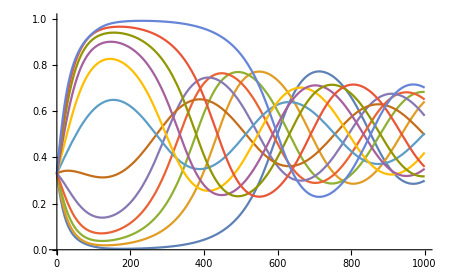

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

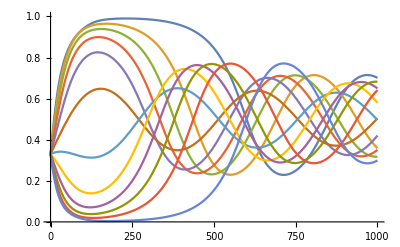

```mathematica
Plot[{v2series},{t,0,1000},PlotRange -> {0,1}]
```

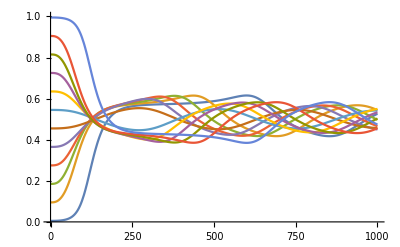

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

This this system results in a limit cycle regardless of the initial frequency of the symbiont. Next, I’ll show that the generalist host always goes extinct when its payoff is sufficiently low based on its parameter values. Note that for the fitness feedback system we found that the raw difference between specialist and generalist parameter values was no longer sufficient to fully explain whether the system cycled, or fixed the generalist.

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[1000]+v2[1000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

The generalist goes extinct, there are no cases in which the population is not entirely composed of the specialist.

Now we will hold symbiont frequency steady and vary the initial frequency of only host 1:

```mathematica
PA=ANT[0.9,0.4,0.2,1,0.5,1,1];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,0.005,0.995,0.09},{v20,{0.33}}, {vg0,{0.33}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Now we’ll plot the frequency of hosts:

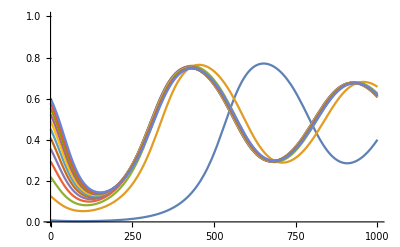

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

And here we’ll plot the frequency of symbionts:

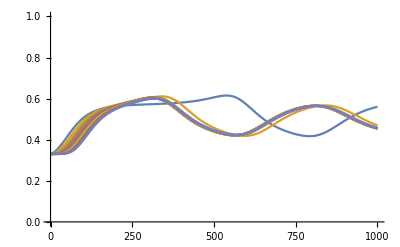

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

So any initial frequency of host 1 leads to a limit cycle.

We’ll check our result that generalists go extinct:

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[1000]+v2[1000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

As expected the generalists are excluded from the limit cycle. Next we vary the initial frequency of symbiont 2:

```mathematica
PA=ANT[0.9,0.4,0.2,1,0.5,1,1];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,10000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,{0.33}},{v20,0.005,0.995,0.09}, {vg0,{0.33}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Now we’ll plot the frequency of hosts:

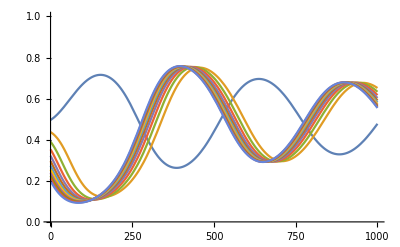

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

Next the symbionts:

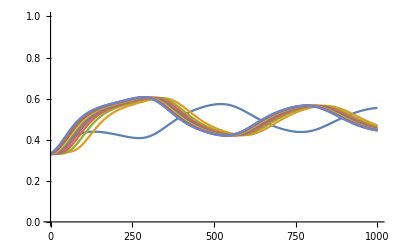

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

Once more we’ll check the frequency of generalists:

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[1000]+v2[1000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

As before generalists go extinct.

Finally, we’ll test the extreme cases when one match or mismatch is extremely likely to fix. These occur when generalists are nearly entirely absent, and hosts and symbiont parings are extremely frequent or infrequent:

```mathematica
PA=ANT[0.9,0.4,0.2,1,0.5,1,1];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.005,0.995}}, {v10,{0.005,0.995}},{v20,{0.005,0.995}}, {vg0,{0.005}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

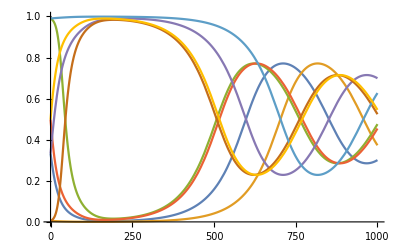

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

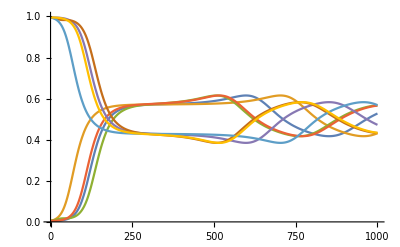

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

These cases too result in limit cycles. Let’s check the frequency of generalists.

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[1000]+v2[1000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{1.,1.,1.,1.,1.,1.,1.,1.}

As before the generalists go extinct, all remaining hosts are specialists of one type or another.

What happens when (π+π’)/2< π_g? Our stability analysis tells us that all hosts will be generalists.

Well first explore this case while varying initial symbiont frequency:

```mathematica
PA=ANT[0.8,0.8,0.2,1,0.5,1,1];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,3000},{u0, v10, v20}];
ICs=Table[{u0,v10,v20},{u0,0.005,0.995,0.09}, {v10,{0.33}},{v20,{0.33}}]~Flatten~2;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

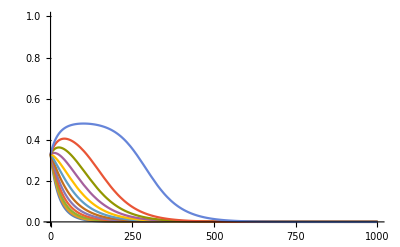

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

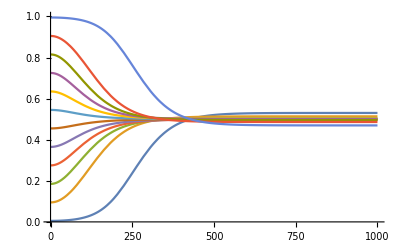

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

The generalist always fixes, and an intermediate symbiont frequency remains.

Now we’ll vary the initial frequency of host 1:

```mathematica
PA=ANT[0.8,0.6,0.2,1,0.5,1,1];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,0.005,0.995,0.09},{v20,{0.05}},{vg0,{0.05}} ]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

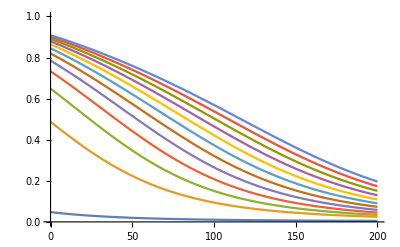

```mathematica
Plot[{v1series},{t,0,200},PlotRange -> {0,1}]
```

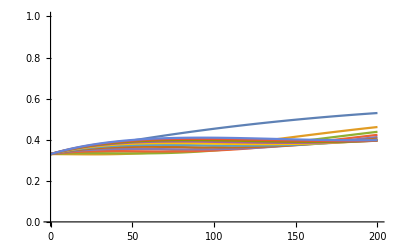

```mathematica
Plot[{useries},{t,0,200},PlotRange -> {0,1}]
```

The symbiont frequency fixes at some stable intermediate value, while all specialist hosts go extinct.

The same occurs in the case in which the frequency of the other specialist host varies.

Finally we consider the cases that are highly favourable to fixation of the specialist, even when generalist payoff exceeds their own:

```mathematica
PA=ANT[0.8,0.6,0.2,1,0.5,1,1];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.005,0.995}}, {v10,{0.005,0.995}},{v20,{0.005,0.995}},{vg0,{0.005}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

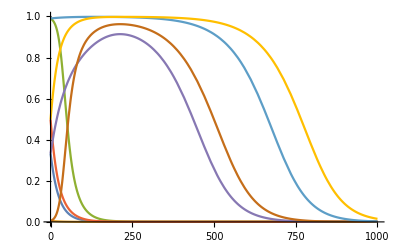

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

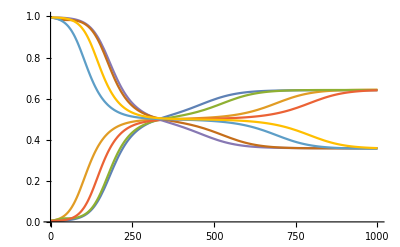

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```